# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
T1-><|"Alice"->100, "Bob"->110 |>,
T2-><|"Alice"->40, "Bob"->45|>,
(* duration for moving operations: Split,Combine, and physical swap*)
DurMove-><|"Alice"->4, "Bob"->5|>,

(*fidelity of preparation/initialisation*)
FidInit-><|"Alice"->0.99, "Bob"->0.98|>,
(*fraction of depolarising:dephasing in the initialisation *)
EFInit-><|"Alice"->{1,0}, "Bob"->{1,0}|>,
DurInit-><|"Alice"->2,"Bob"->5|>,

(* Readout: fidelity. It has bitflip error 
Scattering error affecting the neighborhood qubits, e.g., collaps the superposition into 0
*)
FidRead-><|"Alice"->0.98, "Bob"->0.99|>,
DurRead-><|"Alice"->20, "Bob"->20|>,

(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual)
future:Set manually the error coefficient instead of setting the fidelity at the first place.
Future: off-resonant oscillation in the same zone
 *)
FidSingleXY-><|"Alice"->0.9999, "Bob"->0.99999|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{1,0},"Bob"->{0.9,0.1}|>,

(* rabi frequency on single rotations in MHz *)
RabiFreq-><|"Alice"->5, "Bob"->5 |>,

(* frequency of CZ operation*)
FreqCZ-><|"Alice"->5*10^3,"Bob"->3.3*10^3|>,
(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.97, "Bob"->0.96|>,
EFCZ-><|"Alice"->{1,0},"Bob"->{0,1}|>,
(* frequency of remote entanglement *)
FreqEnt->6*10^3,
(* fidelity of remote entanglement *)
FidEnt->0.8,
EFEnt->{1,0}
};
```

All nodes are simulated in one big density matrix that is paritioned.

T1, and T2 for individual qubits
T1-><|”Alice”-><|1->100,2->101|>, “Bob”->110 |>,
modifyDev[dev,Opts->xxx]. One can modify T1, T2 in between.

Questlink takes initial indices; thus, passive noise is incorrect. Thus, passive noise is manually added for every gate.
Passive noise different on each zone.

Spatial move operations (SplitZ, CombS, PSwap) and quantum operations (the rest) must be done separately to follow the correct zone rules.
CombS, combine string within the zone not yet applied completely? (do one needs to combine string before applying 2-qubit gates?). Can one accidentally perform combine multiple times?  The noise on the move operations? (passive noise)

Correlated noise happens only to qubits with the same zone.

Should SplitZ_(p,q)=SplitZ_(q,p)? (no, split is correct)

ToZone_q operation? see p. 19→20 (shuttle_q____)

The role of measurement/outcome in the sequence?
Measurement involves scattering that can affect neighborhood atoms within raidus.

Exact operations on entangling (forget everything before, then assign it to 01+10

Parrallel -> None, Default (no operations in the same zone, always parallel Alice and Bob, Ent is always serial) , Full (Default+ parallel when in different zone)

native gates :  Init, Read, Rx, Ry, CZ, Ent[node1, node2], SWAPLoc, Splz, Comb  

Zone1 : prepare, store?, detect
Zone2 : prepare, store?, detect, logic
Zone3 : prepare, store?, detect, logic
Zone4 : remote entangle

```mathematica
dev=TrappedIonOxford[];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev=TrappedIonOxford[];
ncirc=InsertCircuitNoise[{Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3]},dev,ReplaceAliases->False];
DrawCircuit@ncirc;
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev@NumAccessibleQubits
```

8

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[8];
ψ=CreateQureg[8];
```

WARNING : the original automatic parallel will mess up the order

```mathematica
qmap=dev[QMap]
```

<|Alice→<|1→0,2→1,3→2,4→3|>,Bob→<|1→4,2→5,3→6,4→7|>|>

```mathematica
circ2=TotalCircTrappedion[circ,dev]
```

{{Splz_(1,2)[Alice,3],Splz_(5,6)[Bob,3]},{Init_2[Alice],Init_6[Bob]},{Init_3[Alice],Init_7[Bob]},{Splz_(2,3)[Alice,4],Splz_(6,7)[Bob,4]},{Ent_(3,7)[Alice,Bob]},{Comb_(2,3)[Alice,3],Comb_(6,7)[Bob,3]},{SWAPLoc_(2,3)[Alice],SWAPLoc_(6,7)[Bob]},{Splz_(3,2)[Alice,4],Splz_(7,6)[Bob,4]},{Ent_(2,6)[Alice,Bob]},{Comb_(3,2)[Alice,3],Comb_(7,6)[Bob,3]},{CZ_(3,2)[Alice],CZ_(7,6)[Bob]},{Splz_(3,2)[Alice,2],Splz_(7,6)[Bob,2]},{Init_0[Alice],Init_4[Bob]},{Read_2[Alice],Read_6[Bob]},{Splz_(0,1)[Alice,2],Splz_(4,5)[Bob,2]},{Init_2[Alice],Init_6[Bob]},{Comb_(1,3)[Alice],Comb_(5,7)[Bob]},{Shutl_2[Alice,4],Shutl_6[Bob,4]},{Shutl_(5,7)[Bob,3]}}

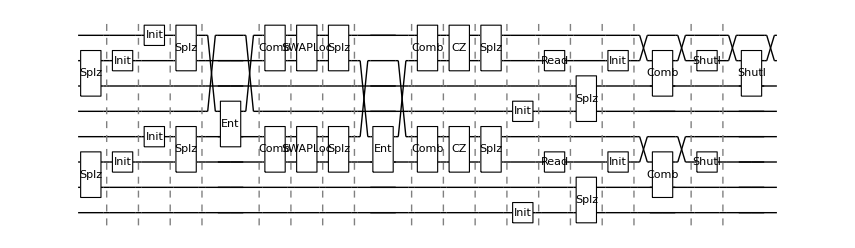

```mathematica
DrawCircuit@circ2
```

```mathematica
InsertCircuitNoise[circ2,TrappedIonOxford[],ReplaceAliases->False]
```

Part::partw: Part 1 of {} does not exist.

Range::range: Range specification in Range[1+Min[3,Missing[KeyAbsent,5]],-1+Max[3,Missing[KeyAbsent,5]]] does not have appropriate bounds.

Table::iterb: Iterator {VQD`Private`z,Range[1+Min[3,Missing[KeyAbsent,5]],-1+Max[3,Missing[KeyAbsent,5]]]} does not have appropriate bounds.

InsertCircuitNoise::error: Encountered gate \*RowBox[{SubscriptBox["Splz", RowBox[{"5", ",", "6"}]], "[", RowBox[{"\"Bob\"", ",", "3"}], "]"}…ue to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

$Failed

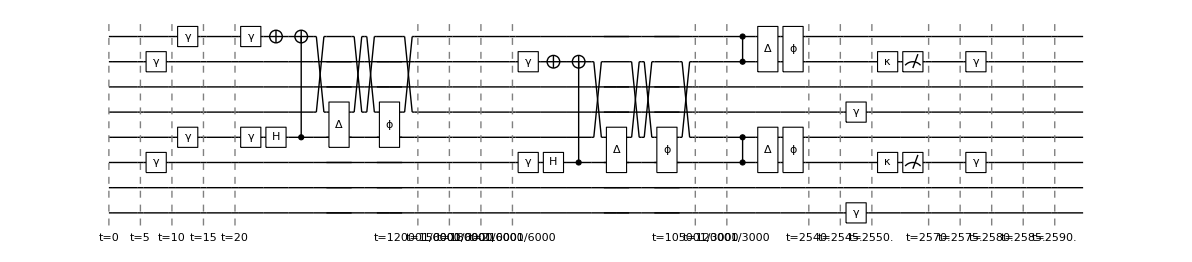

```mathematica
DrawCircuit@%
```

```mathematica
circ={Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Splz, 4,3]["Alice",2],Subscript[Splz, 4,3]["Bob",2],Subscript[Init, 1]["Alice"],Subscript[Init, 1]["Bob"],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Init, 3]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Comb, 2,4]["Alice"],Subscript[Comb, 2,4]["Bob"],Subscript[Shutl, 3]["Alice",4],Subscript[Shutl, 3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[SWAPLoc, 2,4]["Alice"],Subscript[SWAPLoc, 2,4]["Bob"],Subscript[Splz, 4,2]["Alice",3],Subscript[Splz, 4,2]["Bob",3],Subscript[Comb, 2,3]["Alice",3],Subscript[Comb, 2,3]["Bob",3],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 2,3]["Bob"],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 3,2]["Bob",4],
Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",3],Subscript[Comb, 3,2]["Bob",3],Subscript[CZ, 3,2]["Alice"],Subscript[CZ, 3,2]["Bob"]
};
dev=TrappedIonOxford[];
ncirc=InsertCircuitNoise[List/@circ,dev];
DrawCircuit@ncirc;
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TotalCircTrappedion[circuit_,device_,mapindex_:True]:=Module[{circ2=circuit,ccirc={},qmap,quota,col,i,del,parties,gate,entp},
qmap=device[QMap];
parties=Keys@device[Nodes];

While[Length@circ2>0,
col={};del={};
quota=<|Table[p->1,{p,parties}]|>;
Table[(*loop on every parties*)
(* fill up quota on each party *)
If[quota[party]>0,
For[i=1,i<=Length@circ2,i++,
gate=circ2[[i]];
If[(*entangling gate*)
MatchQ[gate,Subscript[Ent, __][__]],
entp=gate/.Subscript[Ent, __][n1_,n2_]:>{n1,n2};
Table[quota[p]-=1,{p,entp}];
AppendTo[col,gate];
AppendTo[del,i];
Break[]
,
(*ordinary gates*)
If[MemberQ[gate,party,-1],
quota[party]-=1;
AppendTo[col,gate];
AppendTo[del,i];
Break[]]
]
];
],{party,parties}];
AppendTo[ccirc,col];
circ2=Delete[circ2,List/@del];
];
If[mapindex,
ccirc/.{
Subscript[Shutl, qs__][n_,z_]:>Subscript[Shutl, Sequence@@Table[qmap[n][q],{q,{qs}}]][n,z],
Subscript[Splz, q1_,q2_][n_,z_]:>Subscript[Splz, qmap[n][q1],qmap[n][q2]][n,z],
Subscript[Comb, q1_,q2_][n_,z_]:>Subscript[Comb, qmap[n][q1],qmap[n][q2]][n,z],
Subscript[Comb, q1_,q2_][n_]:>Subscript[Comb, qmap[n][q1],qmap[n][q2]][n],
Subscript[Ent, q1_,q2_][n1_,n2_]:>Subscript[Ent, qmap[n1][q1],qmap[n2][q2]][n1,n2],
Subscript[CZ, q1_,q2_][n_]:>Subscript[CZ, qmap[n][q1],qmap[n][q2]][n],
Subscript[SWAPLoc, q1_,q2_][n_]:>Subscript[SWAPLoc, qmap[n][q1],qmap[n][q2]][n],
Subscript[Init, q_][n_]:>Subscript[Init, qmap[n][q]][n],
Subscript[Read, q_][n_]:>Subscript[Read, qmap[n][q]][n]
},
ccirc
]
]
```

```mathematica
TotalCircTrappedion[circ,dev,True]
```

{{Splz_(1,2)[Alice,3],Splz_(5,6)[Bob,3]},{Init_2[Alice],Init_6[Bob]},{Init_3[Alice],Init_7[Bob]},{Splz_(2,3)[Alice,4],Splz_(6,7)[Bob,4]},{Ent_(3,7)[Alice,Bob]},{Comb_(2,3)[Alice,3],Comb_(6,7)[Bob,3]},{SWAPLoc_(2,3)[Alice],SWAPLoc_(6,7)[Bob]},{Splz_(3,2)[Alice,4],Splz_(7,6)[Bob,4]},{Ent_(2,6)[Alice,Bob]},{Comb_(3,2)[Alice,3],Comb_(7,6)[Bob,3]},{CZ_(3,2)[Alice],CZ_(7,6)[Bob]},{Splz_(3,2)[Alice,2],Splz_(7,6)[Bob,2]},{Init_0[Alice],Init_4[Bob]},{Read_2[Alice],Read_6[Bob]},{Splz_(0,1)[Alice,2],Splz_(4,5)[Bob,2]},{Init_2[Alice],Init_6[Bob]},{Comb_(1,3)[Alice],Comb_(5,7)[Bob]},{Shutl_2[Alice,4],Shutl_6[Bob,4]},{Shutl_(5,7)[Bob,3]}}

```mathematica
DrawCircuit@%
```

-Graphics-

34

<|Alice→<|1→{1},2→{2,4},3→{3},4→{}|>,Bob→<|1→{1},2→{2,4},3→{3},4→{}|>|>

{3}{}

34

<|Alice→<|1→{1},2→{2,4},3→{},4→{3}|>,Bob→<|1→{1},2→{2,4},3→{3},4→{}|>|>

{3}{}

23

<|Alice→<|1→{1},2→{2,4},3→{},4→{3}|>,Bob→<|1→{1},2→{2,4},3→{},4→{3}|>|>

{2,4}{}

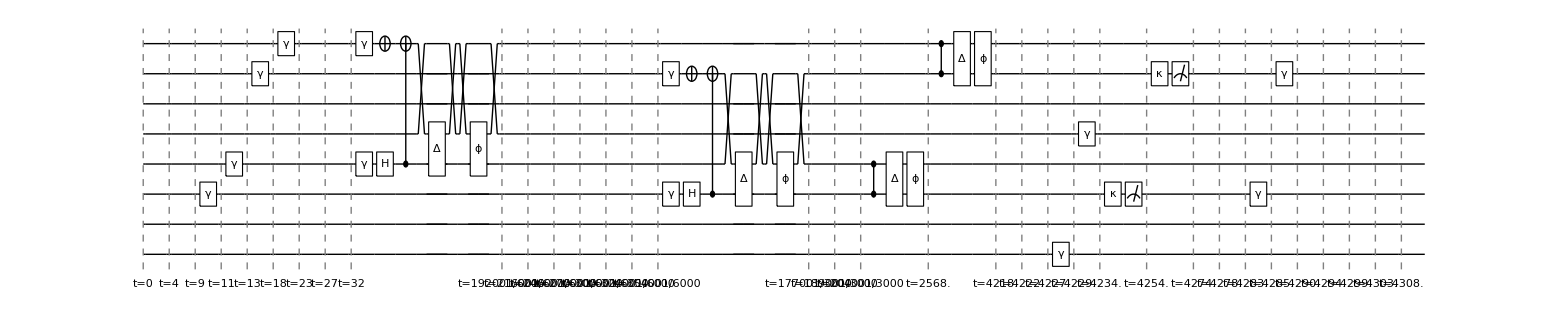

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev=TrappedIonOxford[];
ncirc=InsertCircuitNoise[circ,dev,ReplaceAliases->True];
DrawCircuit@ncirc
dev@ShowNodes
```

```mathematica
Subscript[shutl, 3][nodes,"Bob",4]
```

<|Alice→<|1→{1},2→{2},3→{2,3},4→{}|>,Bob→<|1→{1},2→{2,4},3→{},4→{3}|>|>

```mathematica
nodes
```

<|Alice→<|1→{1},2→{2},3→{2,3},4→{}|>,Bob→<|1→{1},2→{2,4},3→{3},4→{}|>|>

```mathematica
ApplyCircuit[ρ,ExtractCircuit@ncirc]
```

{{0},{1}}

```mathematica
Subscript[Split, 4,2]["Bob",3]
```

Split_(4,2)[Bob,3]

```mathematica
SetQuregMatrix[ρ,RandomMixState[8]];
```

```mathematica
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[circ,TrappedIonOxford[],ReplaceAliases->True]]
```

{{0},{1}}

```mathematica
nodes=Keys@OptionValue[TrappedIonOxford,Nodes]
```

{Alice,Bob}

```mathematica
(*separate circ *)
qmap=<|"Alice"-><|1->0,2->1,3->2,4->3|>,"Bob"-><|1->4,2->5,3->6,4->7|>|>;
```

```mathematica
circ
```

```mathematica
{Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Splz, 4,3]["Alice",2],Subscript[Splz, 4,3]["Bob",2],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Init, 3]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Comb, 2,4]["Alice"]}
```

```mathematica
DrawCircuit@circ
```

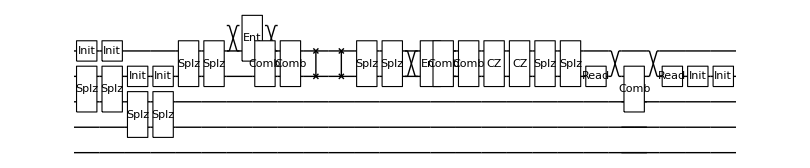

```mathematica
circ2=circ/.{
Subscript[Ent, p_,q_][n1_,n2_]:>Subscript[Ent, qmap[n1][p],qmap[n2][q]][n1,n2],
Subscript[g_, p_,q_][n_,z_Integer]:>Subscript[g, qmap[n][p],qmap[n][q]][n,z],
Subscript[g_, q_][n_]:>Subscript[g, qmap[n][q]][n],
Subscript[g_, p_,q_][n_]:>Subscript[g, qmap[n][p],qmap[n][q]][n]
};
```

```mathematica
DrawCircuit@%
```

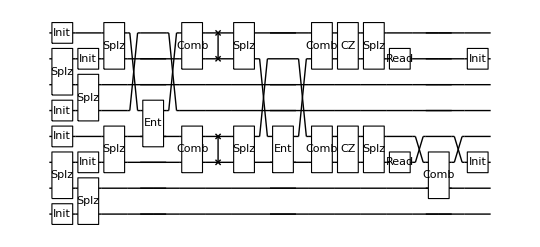

```mathematica
circcols=GetCircuitColumns@circ2;
```

```mathematica
DrawCircuit@circ2
```

```mathematica
circ2=Flatten@circcols
```

```mathematica
{Subscript[Splz, 1,2]["Alice",3],Subscript[Splz, 5,6]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 7]["Bob"],Subscript[Init, 0]["Alice"],Subscript[Init, 4]["Bob"],Subscript[Init, 2]["Alice"],Subscript[Init, 6]["Bob"],Subscript[Splz, 0,1]["Alice",2],Subscript[Splz, 4,5]["Bob",2],Subscript[Splz, 2,3]["Alice",4],Subscript[Splz, 6,7]["Bob",4],Subscript[Ent, 3,7]["Alice","Bob"],Subscript[Comb, 2,3]["Alice",3],Subscript[Comb, 6,7]["Bob",3],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 6,7]["Bob"],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 7,6]["Bob",4],Subscript[Ent, 2,6]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",3],Subscript[Comb, 7,6]["Bob",3],Subscript[CZ, 3,2]["Alice"],Subscript[CZ, 7,6]["Bob"],Subscript[Splz, 3,2]["Alice",2],Subscript[Splz, 7,6]["Bob",2],Subscript[Read, 2]["Alice"],Subscript[Read, 6]["Bob"],Subscript[Comb, 1,3]["Alice"],Subscript[Init, 2]["Alice"],Subscript[Init, 6]["Bob"]}
```

```mathematica
tonode={
Subscript[Ent, p_,q_][n1_,n2_]:>Ent,
Subscript[g_, p_,q_][n_,z_Integer]:>n,
Subscript[g_, q_][n_]:>n,
Subscript[g_, p_,q_][n_]:>n
}
```

{Ent_(p_,q_)[n1_,n2_]:>Ent,g__(p_,q_)[n_,z_Integer]:>n,g__q_[n_]:>n,g__(p_,q_)[n_]:>n}

```mathematica
oldcirc=circ2;
newcirc=
While[Length@oldcirc>0,
	quota=<|#->True&/@nodes|>;
	col={};
	todel={};
For[i=1,i<=Length@oldcirc,i++,
	gate=oldcirc[[1]];
	node=gate/.tonode;
	If[node===Ent,
	AppendTo[col,gate];
	AppendTo[todel,i];
	Break[]
       ];
If[quota[node],
AppendTo[col,gate];
AppendTo[todel,i];
quota[node]=False
];
If[¬Or@@Values[quota],
Break[]
]
];
oldcirc=Delete[oldcirc,todel];
Print@col
]
```

{Splz_(1,2)[Alice,3]}

{Splz_(5,6)[Bob,3]}

{Init_3[Alice]}

{Init_7[Bob]}

{Init_0[Alice]}

{Init_4[Bob]}

{Init_2[Alice]}

{Init_6[Bob]}

{Splz_(0,1)[Alice,2]}

{Splz_(4,5)[Bob,2]}

{Splz_(2,3)[Alice,4]}

{Splz_(6,7)[Bob,4]}

{Ent_(3,7)[Alice,Bob]}

{Comb_(2,3)[Alice,3]}

{Comb_(6,7)[Bob,3]}

{SWAPLoc_(2,3)[Alice]}

{SWAPLoc_(6,7)[Bob]}

{Splz_(3,2)[Alice,4]}

{Splz_(7,6)[Bob,4]}

{Ent_(2,6)[Alice,Bob]}

{Comb_(3,2)[Alice,3]}

{Comb_(7,6)[Bob,3]}

{CZ_(3,2)[Alice]}

{CZ_(7,6)[Bob]}

{Splz_(3,2)[Alice,2]}

{Splz_(7,6)[Bob,2]}

{Read_2[Alice]}

{Read_6[Bob]}

{Comb_(1,3)[Alice]}

{Init_2[Alice]}

{Init_6[Bob]}

```mathematica
newcirc
```